```mathematica
Refine[((k(k+1))/2)^2+(k+1)^3==(((k+1)(k+2))/2)^2,k∈Integers]
```

True

```mathematica
Refine[((k(k+1))/2)^2+(k+1)^3
==((k(k+1))/2)^2+(4(k+1)^3)/4
==(k(k+1))^2/4+(4(k+1)^3)/4
==((k(k+1))^2+4(k+1)^3)/4
==((k(k+1))^2+4(k+1)(k+1)^2)/4
==((k(k+1))^2+4(k+1)(k^2+2k+1))/4
==((k(k+1))^2+4(k^3+3 k^2+3k+1))/4
==((k(k+1))^2+4 k^3+12 k^2+12k+4)/4
==((k^2+k)^2+4 k^3+12 k^2+12k+4)/4
==(k^4+2 k^3+k^2+4 k^3+12 k^2+12k+4)/4
==(k^4+6 k^3+13 k^2+12k+4)/4
== 1/4 k^4+3/2 k^3+13/4 k^2+3k+1
,k∈Integers]//FullSimplify
```

True

```mathematica
Refine[(((k+1)(k+2))/2)^2
==((k+1)(k+2))^2/4
==((k^2+3 k+2)^2)/4
==(k^4+6 k^3+13 k^2+12 k+4)/4
==1/4 k^4+3/2 k^3+13/4 k^2+3k+1 
,k∈Integers]//FullSimplify
```

True

```mathematica
RSolve[f[0]==0,f[n]==-f[n-1]]
```

```mathematica
Module[{f,g},
f[n_]:=Piecewise[{{1, n== 0}, {-f[n-1], n≥1}}];
g[n_]:=(-1)^n;
Show[
ListPlot[Table[{n,f[n]},{n,0,5}]],
ListPlot[Table[{n,g[n]},{n,0,5}]]];
Equal@@Table[With[{f0=f[n],g0=g[n]},f0==g0],{n,0,10}];
Print[FindSequenceFunction[Table[f[n],{n,0,10}],n]];
Print[Table[f[n],{n,0,10}]];
]
```

(-1)^(1+n)

{1,-1,1,-1,1,-1,1,-1,1,-1,1}

True

{1,0,2,2,0,4,4,0,8,8,0,16,16,0,32,32}

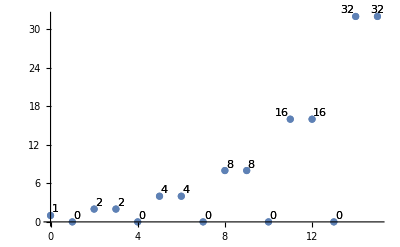

```mathematica
Module[{f,g},
f[n_]:=Piecewise[{{1, n==0}, {0, n==1}, {2, n==2}, {2f[n-3], n≥3}}];
g[n_]:=Piecewise[{{1, n==0}, {0, Mod[n,3]==1}, {2^(Floor[(n-1)/3]+1), True}}];
Print[Equal@@Table[With[{f0=f[n],g0=g[n]},f0==g0],{n,0,10}]];
Print[Table[f[n],{n,0,15}]];
Show[
ListPlot[Table[Labeled[{n,f[n]},f[n]],{n,0,15}]],
ListPlot[Table[Labeled[{n,g[n]},f[n]],{n,0,15}]]
]]
```

```mathematica
f[n_]:=Piecewise[{{1, n==0}, {0, Mod[n,3]==1}, {2^(Floor[(n-1)/3]+1), True}}];
Table[f[n],{n,0,15}]
```

{1,0,2,2,0,4,4,0,8,8,0,16,16,0,32,32}

```mathematica
a[n_]:=4n-2
Table[a[n],{n,1,5}]
```

{2,6,10,14,18}

```mathematica
f[n_]:=Piecewise[{{2, n==1}, {f[n-1]+4, True}}];
Table[f[n],{n,1,5}]
```

```mathematica
{2,6,10,14,18}
```

```mathematica
Piecewise[{{1, n==0}, {0, Mod[n,3]==1}, {2^(Floor[(n-1)/3]+1), True}}]//TeXForm
```

\begin{cases}
 1 & n=0 \\
 0 & (n \bmod 3)=1 \\
 2^{\left\lfloor \frac{n-1}{3}\right\rfloor +1} & \text{True}
\end{cases}

```mathematica
f[n_]:=Piecewise[{{0, n==0}, {1, n==1}, {2f[n-1], True}}];
Table[f[n],{n,0,15}]
```

{0,1,2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384}

```mathematica
FindSequenceFunction[{1,2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384},n]
```

DifferenceRoot[Function[{y,n},{-2 y[n]+y[1+n]==0,y[1]==0,y[2]==1}]][n]

```mathematica
g[n_]:=Piecewise[{{0, n==0}, {2^(n-1), n≥1}}]
Table[g[n],{n,0,15}]
```

{0,1,2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384}

```mathematica
Piecewise[{{0, n==0}, {2^(n-1), n≥1}}]//TeXForm
```

\begin{cases}
 0 & n=0 \\
 2^{n-1} & n\geq 1
\end{cases}

```mathematica
With[{ws=Table[n^2,{n,0,10}]},Print[ws];FindSequenceFunction[ws,n]]//Expand//TraditionalForm
```

{0,1,4,9,16,25,36,49,64,81,100}

n^2-2 n+1

```mathematica
g[n_]:=Piecewise[{{1, n==1}, {g[n-1]+2, n>1}}]
Table[g[n],{n,1,15}]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29}

```mathematica
Select[Table[n,{n,1,15}],OddQ]//DeleteCases[#,OddQ]&
```

{1,3,5,7,9,11,13,15}

```mathematica
exp[a_,1]:=a
exp[a_,n_]:=a*exp[a,n-1]
f[a_,n_]:=exp[a,exp[2,n]]
```

```mathematica
3^(2^5)
```

1853020188851841

```mathematica
exp[3,exp[2,5]]
```

1853020188851841

```mathematica
3^5
```

243

```mathematica
Hold[{exp[a,1]==a,
exp[a,n]==a*exp[a,n-1],
f[a,n]==exp[a,exp[2,n]]}]//TeXForm
```

\text{Hold}[\{\exp (a,1)=a,\exp (a,n)=a \exp (a,n-1),f(a,n)=\exp (a,\exp (2,n))\}]